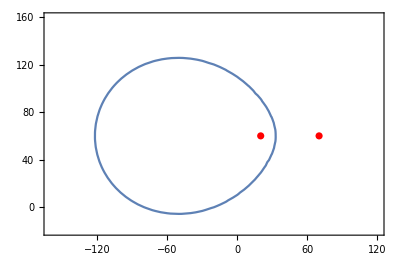

```mathematica
xx = {20, 70};
yy = {60, 60};
data = Transpose@{xx,yy};
p1 = ListPlot[data, PlotStyle->Red];
p2= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0},
{x,-160,120},{y,-20,160}];
s = Show[p2, p1, AspectRatio->Automatic]
```